# Calculating organism heading

## Determining the “front” directions from the positions of the cells’s neighbors - Joakim Johansson

## Two dimensions

First we need a way to plot vectors:

```mathematica
PlotVector[l_]:=Graphics[Arrow[{{0,0},#}]&/@l,PlotRange->{{-2,2},{-2,2}},
Axes->True];
```

Calculate base vectors of transformed base from neighbor vectors. (And thereby transformation matrix)

```mathematica
getTransform[right_,front_,left_,back_]:=
{
Normalize[right-left],
Normalize[front-back]
}
```

Initialize neighbor vectors as rotated π/3 radians:

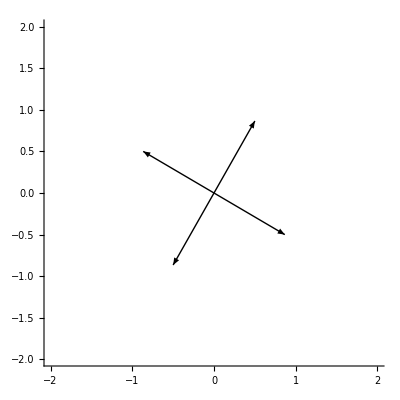

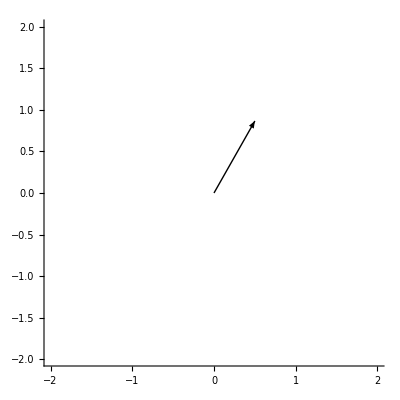
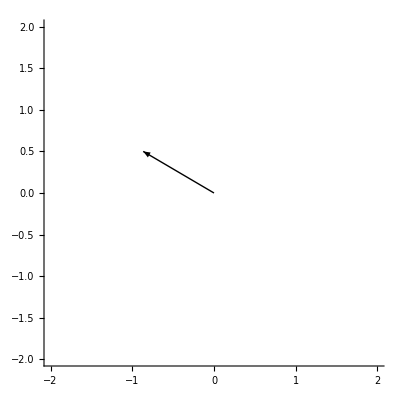
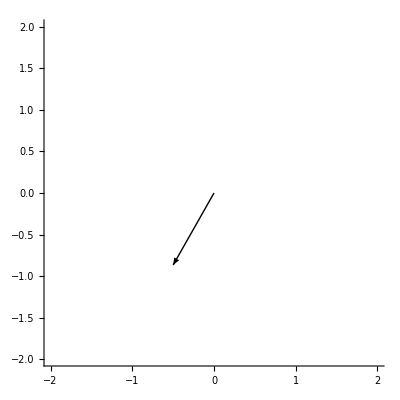
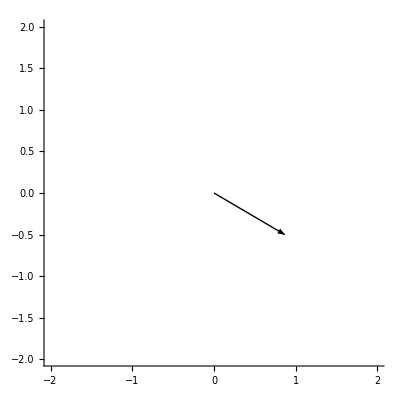

```mathematica
{rotRight,rotFront,rotLeft,rotBack}=RotationMatrix[π/3].#&/@{
{1,0},{0,1},{-1,0},{0,-1}
};
PlotVector[{rotRight,rotFront,rotLeft,rotBack}]
PlotVector[{#}]&/@{rotRight,rotFront,rotLeft,rotBack}
```

Calculate transformational matrix M:

(1/2 | (√3)/2
-(√3)/2 | 1/2)

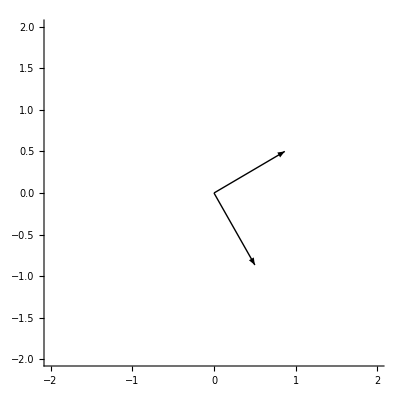

```mathematica
M=getTransform[rotRight,rotFront,rotLeft,rotBack];
M//MatrixForm
PlotVector[M//Transpose]
```

```mathematica
Manipulate[PlotVector[{{x,y},M.{x,y}}],{x,-1,1},{y,-1,1}]
```

## Three dimensions

First we need a way to plot vectors in 3d:

```mathematica
PlotVector3D[l_]:=Graphics3D[Arrow[{{0,0,0},#}]&/@l,
Axes->True];
```

Calculate base vectors of transformed base from neighbor vectors. (And thereby transformation matrix)

```mathematica
getTransform3D[xPlus_,xMinus_,yPlus_,yMinus_,zPlus_,zMinus_]:=
{
Normalize[xPlus-xMinus],
Normalize[yPlus-yMinus],
Normalize[zPlus-zMinus]
}
```

Initialize neighbor vectors as slightly perturbed:

```mathematica
{xPlus,xMinus,yPlus,yMinus,zPlus,zMinus}=(0.2RandomReal[]+#)&/@
{
{1,0,0},{-1,0,0},
{0,1,0},{0,-1,0},
{0,0,1},{0,0,-1}
};
PlotVector3D[{xPlus,xMinus,yPlus,yMinus,zPlus,zMinus}]
```

-Graphics3D-

Calculate transformational matrix M:

```mathematica
𝕄=getTransform3D[xPlus,xMinus,yPlus,yMinus,zPlus,zMinus];
𝕄//MatrixForm
PlotVector3D[𝕄//Transpose]
```

(0.99884 | 0.0340479 | 0.0340479
-0.0470861 | 0.99778 | -0.0470861
-0.0426775 | -0.0426775 | 0.998177)

-Graphics3D-

```mathematica
Manipulate[PlotVector3D[{{x,y,z},𝕄.{x,y,z}}],{x,-1,1},{y,-1,1},{z,-1,1}]
```

Finally, what is the rule for dot product now again?

```mathematica
{
{a.x,a.y,a.z},
{b.x,b.y,b.z},
{c.x,c.y,c.z}
}.{v.x,v.y,v.z}
```

{a.x v.x+a.y v.y+a.z v.z,b.x v.x+b.y v.y+b.z v.z,c.x v.x+c.y v.y+c.z v.z}